# Simulating kinetics of protocell type particles

#### Abhishek Sharma BioMIP, Ruhr Universität, Bochum Germany @ Truce Summer School, 2014

## References

1) Minimal Replicator Theory I: Parabolic Versus Exponential Growth
Günter von Kiedrowski,  
Bioorganic Chemistry Frontiers Volume 3, 1993, pp 113-146

2) PACE project report, http://www.istpace.org/Web_Final_Report/scientific_meetings_at_eclt/workshops/first_year_nov_2004_-_march/protocells_experiments_ethi.html

## Self replicating chemistry using single reactant

```mathematica
ψ[u_]:= 2/u(√(1+u)-1)
```

```mathematica
eq[α_]:=c'[t]== α c[t]ψ[c[t]]
```

```mathematica
ic=c[0]== 10;
```

```mathematica
sol=NDSolve[{eq[1],ic},c[t],{t,0,10}]
```

{{c[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

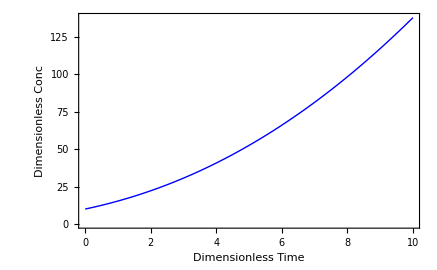

```mathematica
Plot[c[t]/.sol,{t,0,10},PlotStyle-> {Blue,Thick},Frame-> True,FrameLabel-> {"Dimensionless Time","Dimensionless Conc"},BaseStyle->{FontWeight->"Bold",FontSize->10}]
```

## Self replicating chemistry for protocells

```mathematica
eq1[{Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_}]:=c'[t]== Ka1 ac[t]-Ka2 a[t]c[t]+ Kb1 bc[t] -Kb2 b[t]c[t] + 2Kd2 c2[t]-2 Kd1 (c[t])^2
```

```mathematica
eq2[Ka1_,Ka2_,ap_]:= ac'[t]==Ka2 a[t]c[t]-Ka1 ac[t]-ap ac[t]b[t];
```

```mathematica
eq3[Kb2_,Kb1_,app_]:= bc'[t]== Kb2 b[t]c[t]-Kb1 bc[t]-app bc[t]a[t];
```

```mathematica
eq4[f1_,f2_,ap_,app_]:=c2s'[t]==f1 c2[t]-f2 c2s[t]+ap ac[t]b[t]+ app bc[t]a[t];
```

```mathematica
eq5[f1_,f2_,Kd1_,Kd2_]:= c2'[t]== f2 c2s[t]-f1 c2[t]-Kd2 c2[t]+Kd1 c[t]^2
```

```mathematica
eq6[Ka1_,Ka2_,app_]:= a'[t]== Ka1 ac[t]-Ka2 a[t]c[t]-app bc[t]a[t];
```

```mathematica
eq7[Kb1_,Kb2_,app_]:=b'[t]== Kb1 bc[t]-Kb2 b[t]c[t]-app ac[t]b[t];
```

```mathematica
eqns[{Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_,f1_,f2_,ap_, app_}]:={eq1[{Ka1,Ka2,Kb1,Kb2,Kd1,Kd2}],eq2[Ka1,Ka2,ap],eq3[Kb2,Kb1,app],eq4[f1,f2,ap,app],eq5[f1,f2,Kd1,Kd2],eq6[Ka1,Ka2,app],eq7[Kb1,Kb2,app]}
```

```mathematica
iCons:= {a[0]== 1,b[0]== 1,c[0]== 0.01,c2[0]== 0,c2s[0]== 0,ac[0]== 0,bc[0]== 0};
```

```mathematica
totEqns[{Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_,f1_,f2_,ap_, app_}]:= {eqns[{Ka1,Ka2,Kb1,Kb2,Kd1,Kd2,f1,f2,ap, app}],iCons}
```

```mathematica
sol=NDSolve[totEqns[{1,0.1,1,0.1,1,1,1,1,0.1,0.1}],{a[t],b[t],c[t],c2[t],c2s[t],ac[t],bc[t]},{t,0,2000}]
```

{{a[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],b[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],c[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],c2[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],c2s[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],ac[t]→InterpolatingFunction[{{0., 2000.}}, <>][t],bc[t]→InterpolatingFunction[{{0., 2000.}}, <>][t]}}

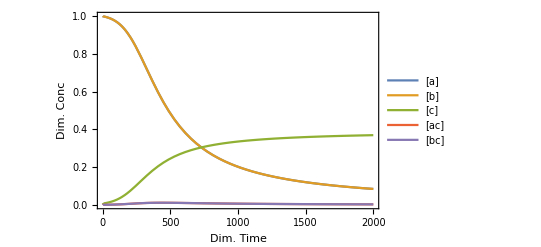

```mathematica
Plot[Evaluate[{a[t],b[t],c[t],ac[t],bc[t]}/.sol],{t,0,2000},PlotStyle-> Thick,PlotLegends->{"[a]","[b]","[c]","[ac]","[bc]"},Frame-> True,PlotRange-> Full,FrameLabel-> {"Dim. Time","Dim. Conc"},BaseStyle->{FontWeight->"Bold",FontSize->10}]
```

## Coupling between two protocells

Consider two particles, which were initially spatially separated. After doing sopme random walks, they came close to each other and start interacting with each other. Due to the presence of two different compartments, the rate equations needs to be modified with a transport term, so and to be solved together so that we can keep track of the concentrations of various species in different compartments.

So, the governing equations in the first compartment is given by :
(The species present in this compartment are “a”, “b”)

```mathematica
eqC11[ϕ_]:=aC1'[t]==-ϕ (aC1[t]-aC2[t])
```

```mathematica
eqC12[ϕ_]:=bC1'[t]==-ϕ(bC1[t]-bC2[t])
```

The equations for the second compartment are given by : 
(The species present in this compartment are “a”, “b”, “c”, “c2”,“ac”, “bc”,”cs”)

```mathematica
eqC21[{Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_}]:=c'[t]== Ka1 ac[t]-Ka2 aC2[t]c[t]+ Kb1 bc[t] -Kb2 bC2[t]c[t] + 2Kd2 c2[t]-2 Kd1 (c[t])^2
```

```mathematica
eqC22[Ka1_,Ka2_,ap_]:= ac'[t]==Ka2 aC2[t]c[t]-Ka1 ac[t]-ap ac[t]bC2[t];
```

```mathematica
eqC23[Kb2_,Kb1_,app_]:= bc'[t]== Kb2 bC2[t]c[t]-Kb1 bc[t]-app bc[t]aC2[t];
```

```mathematica
eqC24[f1_,f2_,ap_,app_]:=c2s'[t]==f1 c2[t]-f2 c2s[t]+ap ac[t]bC2[t]+ app bc[t]aC2[t];
```

```mathematica
eqC25[f1_,f2_,Kd1_,Kd2_]:= c2'[t]== f2 c2s[t]-f1 c2[t]-Kd2 c2[t]+Kd1 c[t]^2
```

```mathematica
eqC26[ϕ_,Ka1_,Ka2_,app_]:= aC2'[t]== Ka1 ac[t]-Ka2 aC2[t]c[t]-app bc[t]aC2[t]+ϕ (aC1[t]-aC2[t]);
```

```mathematica
eqC27[ϕ_,Kb1_,Kb2_,app_]:=bC2'[t]== Kb1 bc[t]-Kb2 bC2[t]c[t]-app ac[t]bC2[t]+ϕ (aC1[t]-aC2[t]);
```

```mathematica
eqns[{ϕ_,Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_,f1_,f2_,ap_, app_}]:={eqC11[ϕ],eqC12[ϕ],eqC21[{Ka1,Ka2,Kb1,Kb2,Kd1,Kd2}],eqC22[Ka1,Ka2,ap],eqC23[Kb2,Kb1,app],eqC24[f1,f2,ap,app],eqC25[f1,f2,Kd1,Kd2],eqC26[ϕ,Ka1,Ka2,app],eqC27[ϕ,Kb1,Kb2,app]}
```

```mathematica
iCons:= {aC1[0]== 1,bC1[0]== 1,aC2[0]== 0,bC2[0]== 0,c[0]== 0.01,c2[0]== 0,c2s[0]== 0,ac[0]== 0,bc[0]== 0};
```

```mathematica
totEqns[{ϕ_,Ka1_,Ka2_,Kb1_,Kb2_,Kd1_,Kd2_,f1_,f2_,ap_, app_}]:= {eqns[{ϕ,Ka1,Ka2,Kb1,Kb2,Kd1,Kd2,f1,f2,ap, app}],iCons}
```

```mathematica
totEqns[{ϕ,Ka1,Ka2,Kb1,Kb2,Kd1,Kd2,f1,f2,ap, app}]//Flatten//MatrixForm;
```

```mathematica
sol=NDSolve[totEqns[{0.1,1,0.1,1,0.1,1,1,1,1,0.1,0.1}],{aC1[t],bC1[t],aC2[t],bC2[t],c[t],c2[t],c2s[t],ac[t],bc[t]},{t,0,5000}]
```

{{aC1[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],bC1[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],aC2[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],bC2[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],c[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],c2[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],c2s[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],ac[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],bc[t]→InterpolatingFunction[{{0., 5000.}}, <>][t]}}

```mathematica
p1=Plot[Evaluate[{aC1[t],bC1[t]}/.sol],{t,0,5000},PlotStyle-> Thick,PlotLegends->{"[a]","[b]","[c]","[ac]","[bc]"},Frame-> True,PlotRange-> Full,FrameLabel-> {"Dim. Time","Dim. Conc"},BaseStyle->{FontWeight->"Bold",FontSize->10},PlotLabel-> "Compartment 1"];
```

```mathematica
p2=Plot[Evaluate[{aC2[t],bC2[t],c[t],ac[t],bc[t]}/.sol],{t,0,5000},PlotStyle-> Thick,PlotLegends->{"[a]","[b]","[c]","[ac]","[bc]"},Frame-> True,PlotRange-> Full,FrameLabel-> {"Dim. Time","Dim. Conc"},BaseStyle->{FontWeight->"Bold",FontSize->10},PlotLabel->"Compartment 2"];
```

```mathematica
GraphicsRow[{p1,p2},Frame-> All]
```

-Graphics-